```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];

1/2 (-θL+ArcTan[Sec[θL]^2 Tan[θ]+Tan[θL]])/.{θL->0}
```

1/2 ArcTan[Tan[θ]]

```mathematica
ClearAll[lerpFunc];
Quiet@FindMinimum[NIntegrate[Abs[
		m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1]))-
		Sin[θ1](π/2 m+0.266 m^2)(b1+b2 Log[a1+a2*m])

	],{θ1,0,π/2},{m,0.01,0.5},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],
	{a1,1},{a2,1},{a3,1},{a4,1},{a5,1},{a6,1},{a7,1},{a8,1},{a9,1},
	{b1,1},{b2,1},{b3,1},{b4,1},{b5,1},{b6,1},{b7,1},{b8,1},{b9,1}]
```

{0.0333697,{a1→1.03506,a2→1.39757,a3→1.,a4→1.,a5→1.,a6→1.,a7→1.,a8→1.,a9→1.,b1→1.29011,b2→-0.558019,b3→1.,b4→1.,b5→1.,b6→1.,b7→1.,b8→1.,b9→1.}}

```mathematica
Manipulate[Plot[
	{
		m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1])),
		Sin[θ1](π/2 m+0.266 m^2)(b1+b2 Log[a1+a2*m])/.{a1->1.035063201957492,a2->1.3975720380013779,a3->1.,a4->1.,a5->1.,a6->1.,a7->1.,a8->1.,a9->1.,b1->1.2901137438013603,b2->-0.5580192450195315,b3->1.,b4->1.,b5->1.,b6->1.,b7->1.,b8->1.,b9->1.}
		
	},{θ1,0,π/2}],
	{m,0.01,0.99}]
```

```mathematica
ClearAll[a,b,c];
Quiet@FindMinimum[NIntegrate[Abs[
		(m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1]))/.{θ1->π/2})-
		(b*m+c*m^2)

	],{m,0.01,0.5},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],
	{a,1},{b,1},{c,1}]
```

{0.000419222,{a→1.,b→1.56197,c→0.26636}}

```mathematica
0.2663601848820869/π
```

0.0847851

End Point

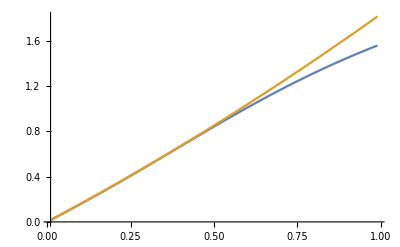

```mathematica
Print[Style["End Point",FontSize->18,Background->Orange]];
Plot[
	{
		m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1]))/.{θ1->π/2},
		π/2 m+0.266 m^2
	},{m,0.01,0.99}]
```

```mathematica
(*ClearAll[a,b,c];
Quiet@FindMinimum[NIntegrate[Abs[
		ArcLength[m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1])),{θ1,0,π/2}]-
		(a+b*m+c*m^2)

	],{m,0.01,0.5},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],
	{a,1},{b,1},{c,1}]*)
```

$Aborted

Bezier t

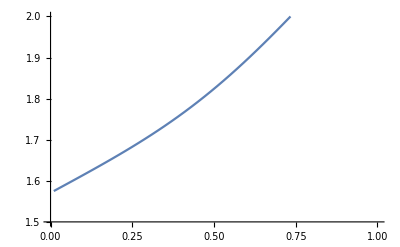

```mathematica
Print[Style["Bezier t",FontSize->18,Background->Orange]];
Plot[ArcLength[m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1])),{θ1,0,π/2}],{m,0.01,0.99},PlotRange->{{0,1},{1.5,2}}]
```

```mathematica
m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1]))/.{θ1->0}
```

0

```mathematica
m (-(m (-1+m^2))/(1+m^2)+(1+m^2) *1)//FullSimplify
```

m+m^3+(m (m-m^3))/(1+m^2)

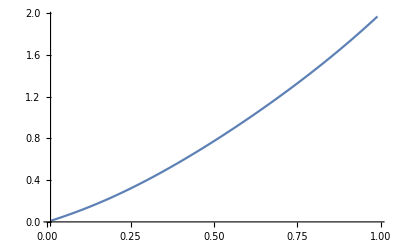

```mathematica
Plot[m+m^3+(m (m-m^3))/(1+m^2),{m,0.01,0.99}]
```

```mathematica
Manipulate[Plot[{
		ArcCot[ m*Cot[θ1/2]],
		(1-m)/m*Sin[θ1]
},{θ1,0,π/2}],
{m,0.01,0.99}]
```

```mathematica
ClearAll[m,θ1];
Series[ArcCot[m Cot[θ1/2]],{Cos[θ1],0,1}]
```

ArcCot[m Cot[θ1/2]]

```mathematica
Series[ArcCot[m *x],{x,0,1}]
```

1/2 (-1)^Floor[(π-Arg[1/m^2]+2 Arg[x])/(2 π)] √(1/m^2) m π+(-m x+O[x]^2)

```mathematica
Manipulate[Plot[
	{
		 ArcCot[m Cot[θ1/2]]
	},{θ1,0,π/2}],
	{m,0.01,0.99}]
```

```mathematica
m ((1+m^2) ArcCot[m Cot[θ1/2]]-(m (-1+m^2) Sin[θ1])/(1+m^2+(-1+m^2) Cos[θ1]))/.{m->0.1}
```

0.1 (1.01 ArcCot[0.1 Cot[θ1/2]]+(0.099 Sin[θ1])/(1.01-0.99 Cos[θ1]))

```mathematica
ClearAll[m,θ,θ1];
Simplify[Integrate[m^4/((1+(-1+m^2) Cos[θ/2]^2)^2),{θ,0,θ1}],0<θ1<π/4]
```

$Aborted

```mathematica
Series[ArcCot[m Cot[ArcCos[x]/2]],{x,1,1}]
```

-1/2 (-1)^Floor[1/2-Arg[m]/π-Arg[Cot[ArcCos[x]/2]]/π] π+1/2 (-1)^Floor[1/2+Arg[Tan[ArcCos[x]/2]/m]/π] π+Tan[(-1)^Floor[-Arg[-1+x]/(2 π)] ((ⅈ √(x-1))/(√2)+O[x-1]^(3/2))]/m-(Tan[(-1)^Floor[-Arg[-1+x]/(2 π)] ((ⅈ √(x-1))/(√2)+O[x-1]^(3/2))]^3)/(3 m^3)

```mathematica
-1/2 π
```

```mathematica
f[n_,j_,u_]:=PiecewiseExpand[BernsteinBasis[n,j,u]]
cv[pt_,n_,u_]:=(f[n,#,u]&/@Range[0,n]).pt
pts={{0,0},{2,4},{4,5},{6,0}};
DynamicModule[{p={{0,0},{2,4},{4,5},{6,0}}},LocatorPane[Dynamic[p],Dynamic@ParametricPlot[cv[p,Length@p-1,v],{v,0,1},Epilog->{Red,PointSize[0.02],Point[p],Green,Line[p]},PlotRange->{0,6}],Appearance->None]]
```

```mathematica
Manipulate[
	Graphics[{BezierCurve[pts,SplineDegree->d],Dashed,Green,Line[pts]},PlotRange->5,Frame->True],

	{{pts,{{-3,0},{-1,3},{1,-3},{3,0}}},Locator,LocatorAutoCreate->True},{{d,3,"degree"},2,6,1}
]
```

```mathematica
Manipulate[Plot[a+b*t+c*t^2,{t,0,1}],
	{{a,0.5},-10,10},
	{{b,0.5},-100,100},
	{{c,1},-100,100}]
```

```mathematica
Manipulate[Plot[2/(1+Exp[-a*(x-b)])-1,{x,0,1},PlotRange->{{0,1},{0,1}}],
	{{a,30},-10,100},
	{{b,0},-10,10},
	{{c,1},1,100}]
```